#### Parameters

```mathematica
(*All constants are linked with NonCentralChi3.pdf generated on Nov 4th, 2015*)
dims=40; (*dimensions => N in PDF*)
si=1.5;  (*max stress intensity => maximum value of parameter l in PDF*)
gamma =2; (* speed of decay function => gamma in the PDF*)
tA=0.75;(*aneuploid dispersion => notation SigmaA in PDF*)
distDecay = 1;(*Speed of decay of the Generalized Gaussian function => notation s in PDF*)
samples =10000;
runningColor = ColorData["CherryTones"][.25];
runningColor=Red;
(*Samples for the Simulated model*)
DesiredDispersion = 1
```

1

#### Functions

```mathematica
mupr[ν_,λ_,n_]:=2^ν Exp[-λ/2]Gamma[ν+n/2]Hypergeometric1F1Regularized[ν+n/2,n/2,λ/2]
mu[k_Integer,γ_,l_,n_,{σA_,s_}]:=
(l^2/s^2)^(k γ)Sum[
Binomial[k,i](-1)^i mupr[γ i,l^2 n/σA^2,n](l^2 n/σA^2)^(-γ i),
{i,0,k}]
mm1=mu[1,γ,l,n,{σA,s}];
ss2=mu[2,γ,l,n,{σA,s}]-mu[1,γ,l,n,{σA,s}]^2//Factor;
```

```mathematica
fMS=Function[l,Evaluate[{mm1,Sqrt[ss2]}/.{n->dims,σA->tA,s->distDecay,γ->gamma}]]; (**)
fM=Function[l,Evaluate[mm1/.{n->dims,σA->tA,s->distDecay,γ->gamma}]];
fS=Function[l,Evaluate[Sqrt[ss2]/.{n->dims,σA->tA,s->distDecay,γ->gamma}]];
 fl[y_]:=Part[FindRoot[fM[x]-y,{x,0.2}],1,2];
```

```mathematica
(*sii is not si by distDecay DANGER!*)
superF1[data_List,dimsi_?NumericQ,sii_?NumericQ,gammai_?NumericQ,tAi_?NumericQ]:=
Module[{fMi,fSi,fli,lsi,smi},
fMi=Apply[Function,{l,Expand[Evaluate[mm1/.{n->dimsi,σA->tAi,s->sii,γ->gammai}]]}];
fSi=Apply[Function,{l,Expand[Evaluate[Sqrt[ss2]/.{n->dimsi,σA->tAi,s->sii,γ->gammai}]]}];
 fli[y_?NumericQ]:=Part[FindRoot[fMi[l]-y,{l,0.2}],1,2];
lsi=Map[fli[First[#]]&,data];
smi = Total[(Map[fSi,lsi]-Map[Last,data])^2];(*value of interest*)
ParametricPlot[{fMi[l],fSi[l]},{l,0.001,si},AxesOrigin->{0,0},PlotRange->{{0,-3},{0,3.5}}];
smi
]

(*sii is not si by distDecay DANGER!*)
plotF1[data_List,dimsi_?NumericQ,sii_?NumericQ,gammai_?NumericQ,tAi_?NumericQ]:=
Module[{fMi,fSi,fli,lsi,smi},
fMi=Apply[Function,{l,Expand[Evaluate[mm1/.{n->dimsi,σA->tAi,s->sii,γ->gammai}]]}];
fSi=Apply[Function,{l,Expand[Evaluate[Sqrt[ss2]/.{n->dimsi,σA->tAi,s->sii,γ->gammai}]]}];
 fli[y_?NumericQ]:=Part[FindRoot[fMi[l]-y,{l,0.2}],1,2];
lsi=Map[fli[First[#]]&,data];
smi = Total[(Map[fSi,lsi]-Map[Last,data])^2];(*value of interest*)
ParametricPlot[{fMi[l],fSi[l]},{l,0.001,si},AxesOrigin->{0,0},PlotRange->{{0,-3},{0,3.5}}] (*correct here*)
]
```

#### Generate Simulated Data

```mathematica
(* Generate a single srtess vector using the 'dim' dimensional uniform distribution, normalize it and make it length 'stresslev'*)
GenerateStress[dim_Integer,stresslev_]:=
Normalize[RandomVariate[UniformDistribution[Table[{-1,1},{dim}]]]]*stresslev
```

```mathematica
(* Generate a 'noaneupl' aneuploid vectors using the 'dim' dimensional normal distribution. The distribution of the vector lengthes in approximately normal with the peak around 'sigmaA' (see the example below) *)
GenerateAneuploidies[dim_Integer,{noaneup_Integer,sigmaA_}]:=
RandomVariate[
MultinormalDistribution[
Table[0,{dim}],
(sigmaA^2/dim)*
IdentityMatrix[dim]
],
noaneup]
```

```mathematica
(* Overrides GenerateAneuploidies method above in case we wont to inject a random variation. In this particular case we assume a uniform distribution on 0, inf with mean of 1 and a standard deviation provided by desired dispersion, hence a log-normal distribution*)
(* GenerateAneuploidies[dim_Integer,{noaneup_Integer,sigmaA_}]:=
RandomVariate[
MultinormalDistribution[
Table[0,{dim}],
(sigmaA^2/dim)*
DiagonalMatrix[
RandomVariate[
LogNormalDistribution[0,DesiredDispersion],
dim]
]
],
noaneup] *)
```

```mathematica
(*Distance transformation function*)
TransFunction[x_] :=
Exp[-x^(2*gamma)/distDecay^(2*gamma)]
```

```mathematica
Plot[TransFunction[x], {x,0,2}];
```

```mathematica
(* Compute the 'r' ratio values distribution for the single stress vector and the set of aneuploid vectors for G=1/(1+d^2) *)
LogRatio[{dS_List,dA_List}]:=
Log[(TransFunction[Norm[dS-dA]]/TransFunction[Norm[dS]])]
```

```mathematica
FindRatioDistribution[dim_Integer,stresslev_,dAset_List,noaneup_Integer]:=
Module[{dS},
dS=GenerateStress[dim,stresslev];
Map[{stresslev,#}&,Take[DeleteCases[Map[LogRatio[{dS,#}]&,dAset],_Complex],noaneup]]
]
```

```mathematica
GenerateRatioDistributionsSet[dim_Integer,{slevmin_,slevmax_,dslev_},dAset_List,noaneup_Integer]:=
Map[FindRatioDistribution[dim,#,dAset,noaneup]&,Range[slevmin,slevmax,dslev]]
```

```mathematica
FindMeanSTD[set_List]:={Part[set,1,1],Mean[Map[Last,set]],StandardDeviation[Map[Last,set]]}
```

```mathematica
MakeLinModel[meanSTDset_List]:=
Module[{set,model,nm},
set=Map[{1,1}Rest[#]&,meanSTDset];
model=LinearModelFit[set,x,x];
nm=Normal[model];
Print[{nm,model["RSquared"]}];
ListPlot[set, 
PlotStyle->{Black},
 AxesLabel->{"mean", "std"}]
]
```

```mathematica
GenerateLinearModelParameters[dim_Integer,{slevmin_,slevmax_,dslev_},dAset_List,noaneup_Integer]:=
Module[{set0,set},
set0=GenerateRatioDistributionsSet[dim,{slevmin,slevmax,dslev},dAset,noaneup];
set=Map[{1,1}Rest[FindMeanSTD[#]]&,set0];
LinearModelFit[set,x,x]["BestFitParameters"]
]
```

```mathematica
Fitness[{dS_List,dA_List}]:=TransFunction[Norm[dA-dS]]
```

```mathematica
(* Generate fitness data set for given aneuploid 'dAset', 'stress' vector and value of the stress magnitude 'stresslev' *)
FitnessDistribution[stresses_List,stresslev_,dA_List,noaneup_Integer]:=
Take[DeleteCases[Map[Fitness[{#,dA}]&,stresses*stresslev],_?Negative],noaneup]
```

```mathematica
MeanFitnessGiniIndex[lst_List]:=
Module[{lstord,len,gini},
lstord=Sort[lst];
len=Length[lst];
gini=Total[Map[(2#-len-1)Part[lstord,#]&,Range[len]]]/(len Total[lst]);
{gini,Mean[lst]}
]
```

#### Match/Mismatch Plot

```mathematica
rendFunction[x_, gamma_,d_] :=
Exp[-x^(2*gamma)/d^(2*gamma)]
```

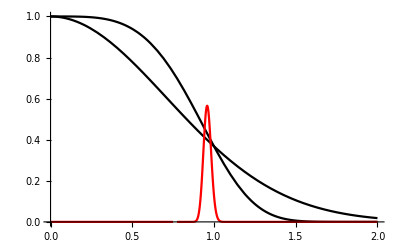

```mathematica
Plot[{rendFunction[x,1,1], rendFunction[x,2,1],
PDF[ChiDistribution[dims]][(x-si*0.5)*dims*tA]},
{x,0,2},
 PlotRange->All,
 PlotStyle->{Black, Black, Red},
AxesStyle->Thick]
```

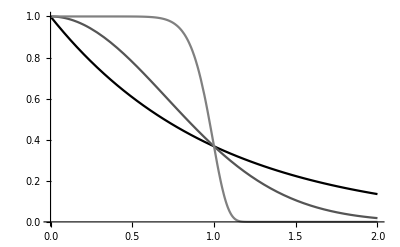

```mathematica
curves=Plot[{rendFunction[x,0.5,1],rendFunction[x,1,1], rendFunction[x,6,1]},
{x,0,2},
PlotRange->{{0,2},{0,1}},
PlotStyle->{Black,Darker[Gray],Gray},
AxesStyle->Thick]
```

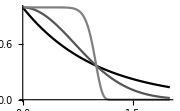

```mathematica
Show[curves,ImageSize->Small]
```

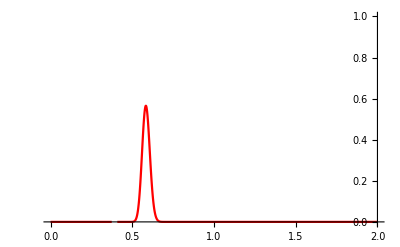

```mathematica
Plot[PDF[ChiDistribution[dims]][(x-si*0.25)*dims*tA],
{x,0,2},
PlotRange->{{0,2},{0,1}},
PlotStyle->Red,
AxesStyle->{{None},{Red,Thick}},
AxesOrigin->{2,0}
]
```

```mathematica
Show[%158,ImageSize->Small]
```

Show::gtype: Symbol is not a type of graphics.

Show[Null,ImageSize→Small]

#### Plot Theoretical Mean - Std

Power::infy: Infinite expression 1/0.^4 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^4 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

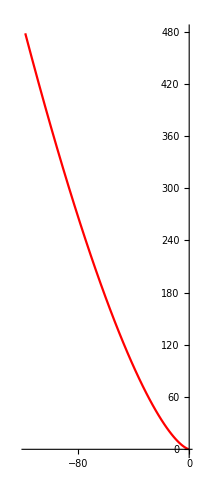

```mathematica
modelPlot=ParametricPlot[{fM[l],fS[l]},
{l,0.0,10},
AxesOrigin->{0,0},
PlotRange->{{0,-1},
{0,1}},
 PlotStyle->runningColor]
```

#### Plot Simulated Mean Std

```mathematica
dAset3=GenerateAneuploidies[dims,{samples,tA}];
```

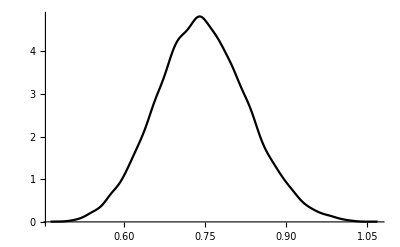

```mathematica
SmoothHistogram[Map[Norm,dAset3],PlotStyle->Black]
```

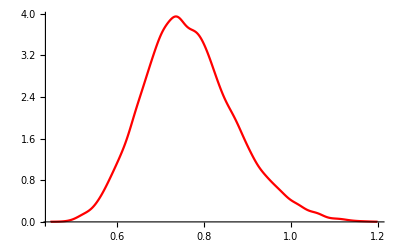

```mathematica
sh2 =SmoothHistogram[Map[Norm,dAset3], PlotStyle->Red]
```

```mathematica
set3=GenerateRatioDistributionsSet[dims,{0.0,si,0.05},dAset3,samples];
```

```mathematica
adderFunction = Function[{pos,mean,std},{pos,mean-std,mean+std}]
adderFunction[1,1,2]
```

Function[{pos,mean,std},{pos,mean-std,mean+std}]

{1,-1,3}

```mathematica
Map[
Apply[adderFunction,FindMeanSTD[#]]&,
set3]
```

{{0.,-0.612183,-0.161058},{0.05,-0.615964,-0.163226},{0.1,-0.629145,-0.168741},{0.15,-0.652192,-0.17766},{0.2,-0.683867,-0.188842},{0.25,-0.719778,-0.207727},{0.3,-0.769002,-0.226824},{0.35,-0.833218,-0.248061},{0.4,-0.894775,-0.276367},{0.45,-0.974251,-0.296588},{0.5,-1.04769,-0.343172},{0.55,-1.15729,-0.365709},{0.6,-1.25539,-0.404373},{0.65,-1.35905,-0.45675},{0.7,-1.4958,-0.481806},{0.75,-1.65031,-0.517919},{0.8,-1.75267,-0.597958},{0.85,-1.9475,-0.614345},{0.9,-2.03679,-0.723515},{0.95,-2.34135,-0.657371},{1.,-2.42255,-0.823847},{1.05,-2.71335,-0.809191},{1.1,-2.87512,-0.88953},{1.15,-3.20948,-0.828252},{1.2,-3.43262,-0.902765},{1.25,-3.72263,-0.926199},{1.3,-3.94539,-1.01635},{1.35,-4.23924,-1.02865},{1.4,-4.68826,-0.960101},{1.45,-4.71858,-1.20859},{1.5,-5.3822,-0.994199}}

```mathematica
divplot = Show[
ListPlot[#,PlotStyle->Black]&/@set3,
ListPlot[Map[Most[FindMeanSTD[#]]&,set3],
PlotStyle->Red,
Joined->True],
ListPlot[Map[Drop[Apply[adderFunction,FindMeanSTD[#]],{2}]&,set3],
PlotStyle->Pink,
Joined->True],
ListPlot[Map[Drop[Apply[adderFunction,FindMeanSTD[#]],{3}]&,set3],
PlotStyle->Pink,
Joined->True],
PlotRange->{{0,si},
{-5,2}},
AxesOrigin->{0,0},
AxesStyle->Thick]
```

-Graphics-

```mathematica
Dimensions[set3]
```

{31,10000,2}

#### Gamma effect

```mathematica
linspace = Prepend[Rest[Range[0,samples+1,samples/10]],1]
```

{1,100,200,300,400,500,600,700,800,900,1000}

```mathematica
group1=Sort[0.5*2^RandomSample[set3[[20,All,2]],10]];
group1bis = Sort[0.5*2^set3[[20,All,2]]][[linspace]];
```

```mathematica
group2=Sort[0.5*2^RandomSample[set3[[20,All,2]],10]];
group2bis = Sort[0.5*2^set3[[20,All,2]]][[linspace]];
```

```mathematica
group3=Sort[0.5*2^RandomSample[set3[[20,All,2]],10]];
group3bis = Sort[0.5*2^set3[[20,All,2]]][[linspace]];
```

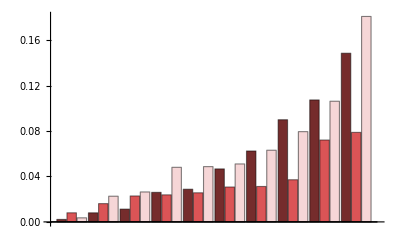

```mathematica
BarChart[
Transpose[
{group1,
group2,
group3}],
ChartStyle->{ColorData["CherryTones"]/@{0.1,.5,.9}},
 ChartLegends->{"","",""},
AxesStyle->Thick]
```

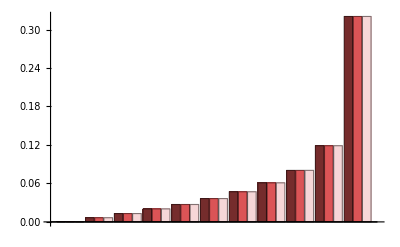

```mathematica
BarChart[
Transpose[
{group1bis,
group2bis,
group3bis}],
ChartStyle->{ColorData["CherryTones"]/@{0.1,.5,.9}},
 ChartLegends->{"","",""},
AxesStyle->Thick]
```

{-0.161881-0.732645 x,0.989402}

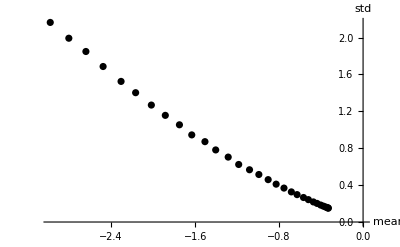

```mathematica
simPlot=MakeLinModel[Map[FindMeanSTD,set3]]
```

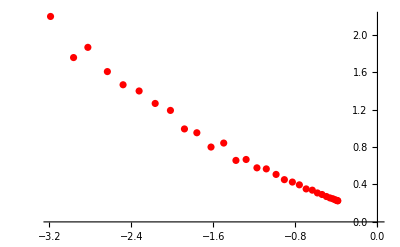

```mathematica
simPlot2=ListPlot[Map[{1,1}Rest[#]&,Map[FindMeanSTD,set3]],PlotStyle->Red]
```

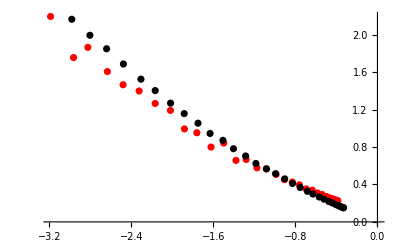

```mathematica
Show[simPlot2, simPlot]
```

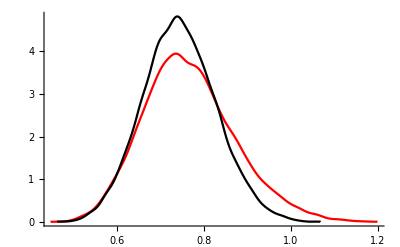

```mathematica
Show[sh2, sh1, PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
mem1 = MakeLinModel[Map[FindMeanSTD,set3]];
```

{0.0123132-0.439868 x,0.991005}

```mathematica
mem2 = MakeLinModel[Map[FindMeanSTD,set3]];
```

{0.0123132-0.439868 x,0.991005}

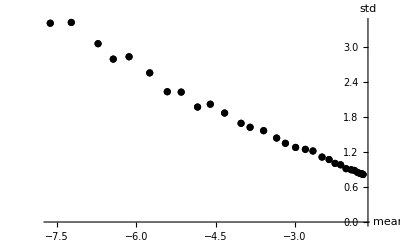

```mathematica
Show[mem1,mem2]
```

#### Combination

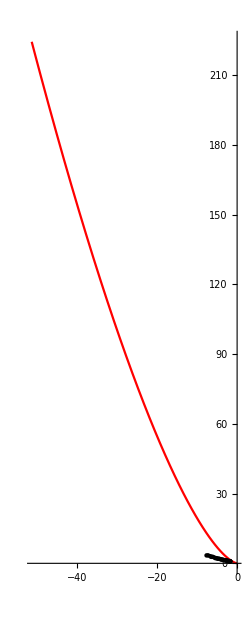

```mathematica
plot1=Show[modelPlot, simPlot, AxesStyle->Thick]
```

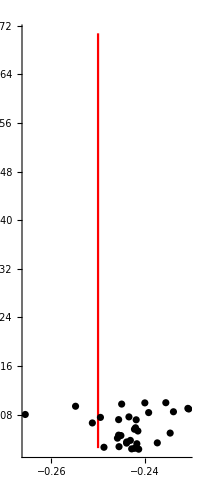

```mathematica
plot2 = Show[modelPlot,simPlot]
```

```mathematica
plot3 = Show[modelPlot,simPlot]
```

-Graphics-

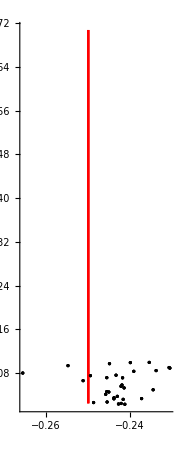

```mathematica
Show[plot1, plot2, plot3,
 PlotRange->{{0,-2},{0,2}},
AxesStyle->Thick,ImageSize->Small]
```

```mathematica
BarLegend[{"CherryTones",{0,1},{.25,.5,.75}}]
```

BarLegend[{CherryTones,{0,1},{0.25,0.5,0.75}}]

```mathematica
BarLegend["CherryTones",{0,.33,.66,1}]
```

#### Tile Plot

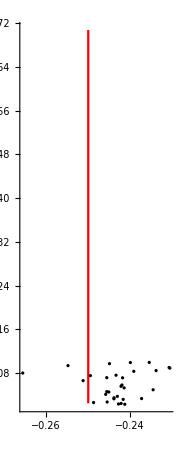

```mathematica
Show[plot1, ImageSize->Small]
```

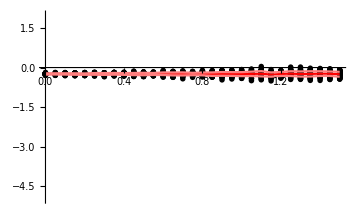

```mathematica
Show[divplot, ImageSize->Medium]
```

## Mean & Gini

#### Functions

```mathematica
(* Generate a single stress vector using the 'dim' dimensional uniform distribution, normalize it and make it length 'stresslev'*)
GenerateStress[dim_Integer,stresslev_]:=
Normalize[RandomVariate[UniformDistribution[Table[{-1,1},{dim}]]]]*stresslev
```

```mathematica
(* Generate a 'noaneupl' aneuploid vectors using the 'dim' dimensional normal distribution. The distribution of the vector lengthes in approximately normal with the peak around 'sigmaA' (see the example below) *)
GenerateAneuploidies[dim_Integer,{noaneup_Integer,sigmaA_}]:=
RandomVariate[MultinormalDistribution[Table[0,{dim}],(sigmaA^2/dim)*IdentityMatrix[dim]],noaneup]
```

```mathematica
(* Compute the fitness for the single stress vector and the aneuploid vector *)
Clear[Fitness]
Fitness[{dS_List,dA_List}]:=TransFunction[Norm[dA-dS]]
```

```mathematica
(* Generate fitness data set for given aneuploid 'dAset', 'stress' vector and value of the stress magnitude 'stresslev' *)
FitnessDistribution[stresses_List,stresslev_,dA_List,noaneup_Integer]:=
Module[{},
Take[DeleteCases[Map[Fitness[{#,dA}]&,stresses*stresslev],_?Negative],noaneup]
]
```

```mathematica
MeanFitnessGiniIndex[lst_List]:=
Module[{lstord,len,gini},
lstord=Sort[lst];
len=Length[lst];
gini=Total[Map[(2#-len-1)Part[lstord,#]&,Range[len]]]/(len Total[lst]);
{gini,Mean[lst]}
]
```

#### Test cell lines

```mathematica
euploid=GenerateAneuploidies[dims,{1,0.07}]//First
```

{0.0137426,0.0229631,0.000488369,-0.0183643,-0.0175479,0.0172875,0.0184335,-0.0022794,0.0208836,0.0238247}

```mathematica
aneuploids=GenerateAneuploidies[dims,{samples,tA}];
```

```mathematica
stresstest=Table[GenerateStress[dims,1],{40}]* RandomReal[{0,1.5},40];
```

#### Test yeast

```mathematica
fitnessdisttest=FitnessDistribution[
stresstest,si,Part[aneuploids,3],20];
```

```mathematica
Norm[stresstest[[1]]]
```

0.368811

```mathematica
FitnessDistribution[
stresstest,0.4,euploid,10]
```

{0.999355,0.998028,0.898066,0.96962,0.957635,0.899215,0.912784,0.999981,0.951652,0.921054}

```mathematica
eutest=MeanFitnessGiniIndex[
FitnessDistribution[
stresstest,0.4,euploid,10]]
```

{0.0230991,0.950739}

```mathematica
restest=Map[MeanFitnessGiniIndex[
FitnessDistribution[
stresstest,0.4,#,10]]&,aneuploids];
```

```mathematica
eutest
```

{0.0230991,0.950739}

```mathematica
restest;
```

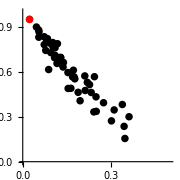

```mathematica
res = ListPlot[restest, PlotStyle->Directive[Black,PointSize[0.03]]];
eu = ListPlot[{eutest},PlotStyle->Directive[Red,PointSize[0.03]]];
Show[res,eu,
 PlotRange->{{0,0.5},{0,1}},
 AxesOrigin->{0,0},
AxesStyle->Thick,
AspectRatio->1,
ImageSize->Small]
```

## Comparison

```mathematica
mem1 = Show[modelPlot, simPlot];
```

```mathematica
mem2 = Show[modelPlot, simPlot];
```

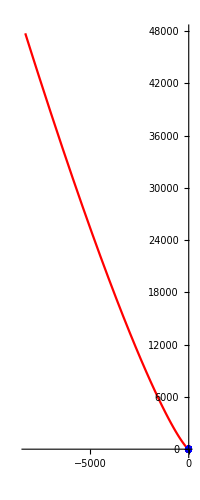

```mathematica
Show[mem1,mem2]
```